# Corner Flow general solution

```mathematica
vx = -B-D*Atan[x,z] + (C*x + D*z)(-x/(x^2+z^2))
vz = A+C*Atan[x,z] + (C*x + D*z)(-z/(x^2+z^2))
```

-B-(x (C x+D z))/(x^2+z^2)-D Atan[x,z]

A-(z (C x+D z))/(x^2+z^2)+C Atan[x,z]

## Apply boundary conditions for continental arc corner flow

```mathematica
x=1
eq1 = ReplaceAll[vx,{Atan[x,z]->0,z->0}]
eq2 = ReplaceAll[vz,{Atan[x,z]->0,z->0}]
eq3=ReplaceAll[vx,{Atan[x,z]->-δ,z->-x*Tan[δ]}]
eq4=ReplaceAll[vz,{Atan[x,z]->-δ,z->-x*Tan[δ]}]
solarc =Solve[eq1==0&&eq2==0&&eq3==Cos[δ]&&eq4==Sin[δ],{A,B,C,D},Reals,Assumptions->{δ>0,δ<Pi/2}]
```

1

-B-C

A

-B+D δ-(C-D Tan[δ])/(1+Tan[δ]^2)

A-C δ+(Tan[δ] (C-D Tan[δ]))/(1+Tan[δ]^2)

{{A→0,B→-(2 Cos[δ]-2 Cos[δ] Cos[2 δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),C→(2 Cos[δ]-2 Cos[δ] Cos[2 δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),D→(2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2)+(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2))/(2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ])}}

```mathematica
ReplaceAll[solarc,{δ->Pi/4}]//FullSimplify
```

{{A→0,B→(2 √2 (4+π))/(-8+π^2),C→-(2 √2 (4+π))/(-8+π^2),D→(2 √2 π)/(-8+π^2)}}

# Plot displacement field

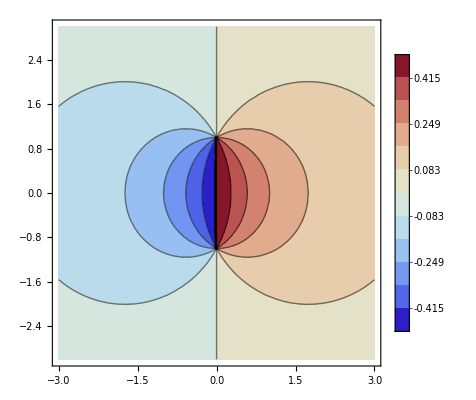

```mathematica
ContourPlot[ReplaceAll[U1d,{w->1}],{x,-3,3},{y,-3,3},ColorFunction->"ThermometerColors",PlotLegends->BarLegend[{Automatic,{-0.5,0.5}}],PlotPoints->20,Contours->11,PlotRange->{-0.5,0.5}]
```

```mathematica
S12 = D[U1d,x]//FullSimplify
S13 = D[U1d,y]//FullSimplify
ContourPlot[ReplaceAll[S12,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,Contours->10]
ContourPlot[ReplaceAll[S13,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,Contours->20]
```

-(w (w^2+x^2-y^2))/(π (x^2+(w-y)^2) (x^2+(w+y)^2))

-(2 w x y)/(π (x^2+(w-y)^2) (x^2+(w+y)^2))